# Little Tests, One pyramidal lvl

## Start

```mathematica
(* Add to path packages *)
packageDirectory=FileNameJoin[{ParentDirectory[ParentDirectory[NotebookDirectory[]]],"1DPackage","*"}]
$Path=Join[$Path,FileNames[packageDirectory]];
```

D:\MastersMathematica\Matematica\MathematicaOpticalFlow\CyclopeanOpticalFlow\1DPackage\*

```mathematica
<<"ReadSintel`"
<<"pyramid1d`"
<<"pyramidalStereoAll`"

methods={"","OverConstrained","SemiConstrained","Constrained","ConstrainedNewMethod"};
Do[
Get["pyramidalCyclope1D"<>met<>"`"]
,{met,methods}]
```

```mathematica
(* Declare path for SINTEL Data depending on user*)

baseSINTEL=Switch[$UserName,
"fieri","D:\\MastersMathematica\\Data\\Sintel",
"roys","/home/roys/datasets/SINTEL-stereo"
];
```

## Data

```mathematica
(* downscaling *)
r=2;
{ia,ib,id,io}=read[baseSINTEL,"Bamboo_1","0001",r,"clean"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Image sections

```mathematica
(*{1,44},{1,102} arbitrary size to make the method faster *)
listDims={{100,100},{150,300},{200,200},{500,300},{500,200}}
ims=Table[
nx=dims[[1]]/r;
ny=dims[[2]]/r;


{iaa,ibb,idd,ioo}=ImageTake[#,{ny,ny+44},{nx,nx+102}]&/@{ia,ib,id,io};
Print[MinMax[Flatten[ImageData[idd]]]];
{iaa,ibb,idd}
,{dims,listDims}]

max=MinMax[Flatten[ImageData[id]]][[2]];
Print["max dv=", max]
```

{{100,100},{150,300},{200,200},{500,300},{500,200}}

{2.17754,38.6009}

{4.70419,12.5952}

{5.09229,7.39881}

{1.91684,28.6525}

{3.36446,26.8223}

{{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-}}

max dv=38.6009

## V0 function

```mathematica
removeClosest[s_]:=Block[{n,c},(n=Nearest[s];
c=SortBy[Table[{i,Norm[s[[i]]-n[s[[i]],2][[2]]]},{i,1,Length[s]}],(#[[2]])&][[1,1]];
Delete[s,c])];
removeClosest[s_]:=s/;Length[s]<2;
```

## Little functions

```mathematica
(*[steps,n,u,listv0,condition,e,{levels},ims]*)
bigTest[steps_,n_,u_,listv0_,condition_,e_,minmaxList_,imslist_]:=Block[{ic,depth, resTable,realPVTable,okTable,realOkPVTable,pos,pv,g0,nonresTable,nonrealPVTable},(
Table[
Table[
depth=stereoDepth[n,u,listv0,condition,im[[1]],im[[2]],minmax[[2]],minmax,Range[1,103,steps],Range[1,45],e,"ConstrainedNewMethod"];

(* We only keep converged solutions *)
resTable=Table[
Select[depth[[r]],#[[2]]=="converged"&]
(*depth[[r]]*)
,{r,45}];

(* We give right coordinates to each solution *)
realPVTable=Table[
pos=resTable[[r,All,5]]-resTable[[r,All,3]];
pv=Thread[{pos,resTable[[r,All,1]]}]
,{r,45}];

(* We only keep ok solutions *)
okTable=Table[
Select[depth[[r]],#[[2]]=="ok"&]
(*depth[[r]]*)
,{r,45}];

(* We give right coordinates to each solution *)
realOkPVTable=Table[
pos=okTable[[r,All,5]]-okTable[[r,All,3]];
pv=Thread[{pos,okTable[[r,All,1]]}]
,{r,45}];

(* We only keep NON converged solutions *)
nonresTable=Table[
Select[depth[[r]],(#[[2]]!="converged"&&#[[2]]!="ok")&]
(*depth[[r]]*)
,{r,45}];

(* We give right coordinates to each solution *)
nonrealPVTable=Table[
pos=nonresTable[[r,All,5]]-nonresTable[[r,All,3]];
pv=Thread[{pos,nonresTable[[r,All,1]]}]
,{r,45}];

(* We create g0 *)
g0=Graphics[{PointSize[0.009],Table[affiche[#,45-y]&/@realPVTable[[y]],{y,1,45}]}];
g0=Rasterize[Show[im[[1]],g0],ImageSize->ImageDimensions[im[[1]]]*5,ImageResolution->300];

{realPVTable,realOkPVTable,nonrealPVTable,g0}

,{minmax,minmaxList}]
,{im, imslist}]
)]
```

## Big Tests

### Test Design

For a synthetical displacement of 0.5:
 
•	Initial values range: {{0,1},{-1,1},{-1,0},{-2,2}}
•	Selection criteria:
	•	We filter direction (positive solutions only)
	•	Range {0, 1} 
	•	No errors allowed
•	Magnitude threshold for gradient is e=0.0001

(* Criterias to select a solution *)

newValCon=Select[tableNewVals,(#[[3]]==”converged”&& #[[1]]*#[[2]]>0 && 0<#[[2]]+#[[1]]<1)&,1];
newValAny=Select[tableNewVals,((#[[3]]≠ “ok”||#[[3]]≠ “oksign”||#[[3]]≠ “okmag”||#[[3]]≠ “converged”)&&#[[1]]*#[[2]]>0 && 0<#[[2]]+#[[1]]<1)&,1];
newValOk=Select[tableNewVals,((#[[3]]==”ok”||#[[3]]==”oksign”||#[[3]]==”okmag”)&& #[[1]]*#[[2]]>0 && 0<#[[2]]+#[[1]]<1)&,1];
noFakeConverge=Select[tableNewVals,(#[[3]]≠ “ok”||#[[3]]≠ “oksign”||#[[3]]≠ “okmag”||#[[3]]≠ “converged”)&,1];

### Test Run

```mathematica
Print["minmax dv=",MinMax[Flatten[ImageData[id]]]]
```

minmax dv={0.136895,38.6009}

```mathematica
(* Test values *)
testLevels={{1,1}};
e=0.0001;
n=0;
u=0;
steps=1;
```

```mathematica
(* Creating list of initial Values *)
range={-5,0};
listv0=Select[RandomReal[range,{1000,2}],(Sign[#[[1]]*#[[2]]]≥0 &&Abs[#[[1]]+#[[2]]]≤ Max[Abs[range]])&];
listv0=Nest[removeClosest,listv0,Length[listv0]-80];
ListPlot[listv0];
```

```mathematica
(* Creating condition *)
topbot={-50,0};
Clear[condition];
condition[x_]:=x[[1]]*x[[2]]>0 && topbot[[1]]<Total[x[[1;;2]]]<topbot[[2]];
```

```mathematica
(* Selection criteria values *)
scale=topbot;
affiche[{p_,v_},y_]:={RainbowColor[Rescale[v,scale,{0,1}]],Point[{p-0.5,y+0.5}]};
RainbowColor[z_]:=Blend[{Purple,Blue,Cyan,Green,Yellow,Orange,Red},z];
legendBar=BarLegend[{RainbowColor,{0,1}},Ticks->Table[{i,Rescale[i,{0,1},scale]},{i,Range[0,1,0.2]}]];
```

```mathematica
levelTable=Table[

bigTest[steps,n,u,listv0,condition,e,{levels},ims]

,{levels,testLevels}];
```

```mathematica
Print["levelTable Dimensions=",Dimensions[levelTable]]
```

levelTable Dimensions={1,5,1,4}

### More numbers

```mathematica
fontsize=16;
```

```mathematica
numbersTable=Table[

solution=ImageData[-ims[[which,3]]];
levelTable[[1,which,1,1]];

density=(Length[Flatten[DeleteDuplicates[#]&/@Floor[levelTable[[1,which,1,1,All,All,1]]]]])/(103.*45.);

vals=Table[
ps=Select[levelTable[[1,which,1,1,y,All,All]],1<Round[#[[1]]]<103&];
(ps[[All,2]]-solution[[y,Round[ps[[All,1]]]]])^2

,{y,Length[levelTable[[1,which,1,1]]]}];

rmse=Sqrt[Mean[Flatten[vals]]];

{Style["RMSE= ",FontSize->fontsize,FontFamily->"Times",Italic],rmse,Style["Density= ",FontSize->fontsize,FontFamily->"Times",Italic],density}

,{which,Length[ims]}]
```

{{RMSE= ,8.99277,Density= ,0.362675},{RMSE= ,2.10489,Density= ,0.43452},{RMSE= ,1.4396,Density= ,0.475944},{RMSE= ,9.02335,Density= ,0.343905},{RMSE= ,3.55881,Density= ,0.423301}}

### Images

```mathematica
Style["Rmse= ",FontSize->fontsize,FontFamily->"Times",Italic]
```

Rmse=

```mathematica
imagesTable=Table[

solution=Image[Table[Map[RainbowColor,imd],{imd,ImageData[Rescale[-ims[[which,3]],scale,{0,1}]]}]];

images=ConformImages[Rasterize[Image[#],ImageResolution->500]&/@Flatten[{ims[[which,1;;2]],levelTable[[1,which,1,4]],solution}],{4000}];

Grid[{images,numbersTable[[which]]}]

,{which,Length[ims]}];
```

```mathematica
imFinal=Legended[Grid[Flatten[{imagesTable},{{2},{1}}]],legendBar]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics-
RMSE=  | 8.99277 | Density=  | 0.362675
-Graphics- | -Graphics- | -Graphics- | -Graphics-
RMSE=  | 2.10489 | Density=  | 0.43452
-Graphics- | -Graphics- | -Graphics- | -Graphics-
RMSE=  | 1.4396 | Density=  | 0.475944
-Graphics- | -Graphics- | -Graphics- | -Graphics-
RMSE=  | 9.02335 | Density=  | 0.343905
-Graphics- | -Graphics- | -Graphics- | -Graphics-
RMSE=  | 3.55881 | Density=  | 0.423301

```mathematica
nbname=StringDelete[Last@FileNameSplit@NotebookFileName[],".nb"];
```

```mathematica
figsDirectory=FileNameJoin[{ParentDirectory[NotebookDirectory[]],"figs"}];

Export[FileNameJoin[{figsDirectory,nbname<>"-im.pdf"}],imFinal]
```

D:\MastersMathematica\Matematica\MathematicaOpticalFlow\CyclopeanOpticalFlow\Figures\figs\sintel-bamboo-clean-im.pdf

### More in depth

```mathematica
lvl=5;
```

```mathematica
k=2;
{ka,kb}=ImageData[#][[k]]&/@ims[[4,1;;2]];
pyra=pyrFuncGen[ka,lvl];
pyrb=pyrFuncGen[kb,lvl];
pyrab=Flatten[{pyra, pyrb},{{2},{1},{3}}];
```

```mathematica
lineTest[n,u,listv0,condition,Range[1,130],pyrab[[1;;1]],e,"ConstrainedNewMethod"]
```

{{0.,0.,sign,1},{0.,0.,sign,2},{0.,0.,sign,3},{0.,0.,sign,4},{-2.16102,-0.800299,ok,5},{0.,0.,sign,6},{-0.283094,-2.57776,ok,7},{-4.84656,-0.684134,converged,8},{-3.96277,-1.48446,converged,9},{-3.06964,-2.3115,converged,10},{-2.14538,-3.20495,converged,11},{-1.13001,-4.23732,converged,12},{-2.25885,-3.22781,converged,13},{-2.59994,-2.83061,converged,14},{0.,0.,sign,15},{0.,0.,sign,16},{0.,0.,sign,17},{0.,0.,sign,18},{-1.78753,-3.91532,converged,19},{-0.779467,-4.93073,converged,20},{-0.16058,-5.48829,ok,21},{0.,0.,sign,22},{-4.02214,-1.83746,converged,23},{-3.98293,-1.8276,converged,24},{-3.26521,-2.54962,converged,25},{-2.41218,-3.40798,converged,26},{-1.71214,-4.11226,converged,27},{-1.27734,-4.52704,converged,28},{-0.507647,-5.27218,converged,29},{-0.0217027,-0.0223853,converged,30},{-1.81371,-0.275928,ok,31},{-5.18881,-0.662219,ok,32},{-2.25189,-1.85967,ok,33},{-3.26393,-0.579252,ok,34},{-3.02363,-0.965518,ok,35},{-1.56412,-2.30088,converged,36},{-0.315557,-3.46213,ok,37},{-0.505817,-1.27568,converged,38},{0.,0.,sign,39},{-7.55548,-2.1168,ok,40},{0.,0.,sign,41},{-5.20137,-5.56216,ok,42},{-4.36445,-22.2189,converged,43},{-3.11217,-23.8037,ok,44},{-2.52161,-12.5479,converged,45},{-1.62045,-24.3605,converged,46},{-0.918406,-24.6802,converged,47},{-1.59675,-10.6389,ok,48},{-0.581793,-10.3536,ok,49},{-0.0998817,-1.32581,converged,50},{-0.0652827,-0.315617,converged,51},{-0.0667381,-0.0687188,converged,52},{-0.260602,-0.120724,converged,53},{-11.7373,-0.806078,ok,54},{0.,0.,sign,55},{0.,0.,sign,56},{-3.05388,-4.1554,ok,57},{-2.04545,-5.198,ok,58},{-7.65178,-2.8574,ok,59},{-10.9868,-2.02984,converged,60},{-9.89498,-3.11708,converged,61},{-9.77124,-3.31916,converged,62},{-8.69268,-4.39002,converged,63},{-7.84432,-5.25273,converged,64},{-8.12808,-4.33095,ok,65},{0.,0.,sign,66},{0.,0.,sign,67},{-12.7704,-0.777151,ok,68},{0.,0.,sign,69},{0.,0.,sign,70},{0.,0.,sign,71},{0.,0.,sign,72},{0.,0.,mag,73},{0.,0.,sign,74},{-0.696039,-1.6114,converged,75},{-0.117778,-0.00646738,ok,76},{-2.20815,-4.13456,ok,77},{0.,0.,mag,78},{-1.1675,-2.84707,ok,79},{-0.318676,-3.5612,converged,80},{-0.545596,-2.39951,converged,81},{-0.0118472,-0.0410844,converged,82},{-5.83624,-0.536856,converged,83},{-2.81059,-1.95119,ok,84},{0.,0.,sign,85},{-1.43203,-0.350062,converged,86},{-0.610539,-1.43026,ok,87},{0.,0.,sign,88},{-3.66708,-2.37841,ok,89},{-2.66689,-3.4604,ok,90},{-1.42457,-7.00926,converged,91},{-2.44159,-5.24482,converged,92},{-1.76753,-12.3104,ok,93},{-0.31259,-7.31012,converged,94},{-1.65514,-1.45752,converged,95},{-0.0728113,-2.57093,converged,96},{0.,0.,sign,97},{0.,0.,sign,98},{-3.51694,-0.366358,converged,99},{-2.0957,-1.50734,converged,100},{0.,0.,sign,101},{0.,0.,sign,102},{0.,0.,sign,103},{0.,0.,sign,104},{0.,0.,sign,105},{0.,0.,sign,106},{0.,0.,sign,107},{0.,0.,sign,108},{0.,0.,sign,109},{0.,0.,sign,110},{0.,0.,sign,111},{0.,0.,sign,112},{0.,0.,sign,113},{-32.6505,-2.45733,ok,114},{-34.6577,-2.65987,ok,115},{-36.8052,-2.86241,ok,116},{-38.739,-3.06475,converged,117},{-40.8081,-3.26716,converged,118},{-42.8876,-3.46952,converged,119},{-44.9752,-3.67187,converged,120},{0.,0.,fakeconverged,121},{0.,0.,fakeconverged,122},{0.,0.,fakeconverged,123},{0.,0.,fakeconverged,124},{0.,0.,fakeconverged,125},{0.,0.,fakeconverged,126},{0.,0.,fakeconverged,127},{0.,0.,fakeconverged,128},{0.,0.,fakeconverged,129},{0.,0.,fakeconverged,130}}

```mathematica
(* Creating list of initial Values *)
range={-3,0};
listv0=Select[RandomReal[range,{1000,2}],(Sign[#[[1]]*#[[2]]]≥0 &&Abs[#[[1]]+#[[2]]]≤ Max[Abs[range]])&];
listv0=Nest[removeClosest,listv0,Length[listv0]-80];
ListPlot[listv0];
```

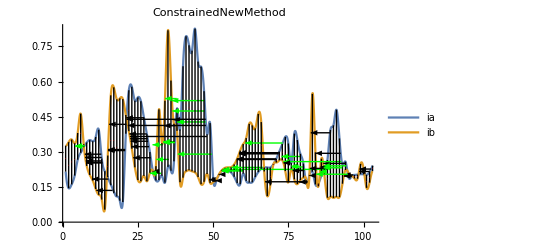

```mathematica
seeAllLine[n,u,listv0,condition,Range[1,103],pyrab[[1;;1]],e,"ConstrainedNewMethod"]
```